# Mathematica Homework III

Cam Hubbard and Brian Carlson 02/18/2014

## Problem 1.

(i) Write a function called uPlusRevTimesOneX[x, low, high] that is given three positive integers as parameters with 
low≤high. The function uPlusRevTimesOneX[x, low,high] returns a list with information about all the {x, y} pairs with the given x value and y values between low and high (inclusive) which satisfy the above condition. A function for checking one pair of x and y values can be found int the class notes from 2/7. Use it  - or some other function you wrote for the same purpose. Each element of the list to be returned by uPlusRevTimesOneX contains the following information: {x,y,x+y,x y}. 

(ii) Write a function called uPlusReverseTimes[low,high] that is given two positive integers as parameters and that returns a list with information about all the candidates with x and y values between low and high (inclusive) which satisfy the above condition. This function must repeatedly use the function uPlusRevTimesOneX.

### Part (i)

#### Test Cases for (i)

### Part (ii)

#### Test Cases for (ii)

## Problem 2.

(i)  Create a function uRandomCircles[n, xbound, ybound] which has three positive parameters; n is an integer. The function creates and returns a list (called circlelist) with n elements. Each element in the list describes a circle using three values {{xcenter,ycenter},rad} where {xcenter,ycenter} is the center of the circle and rad is the radius. Note that the circle must fit within the rectangle R = [-xbound, xbound] × [-ybound,ybound].
The centers and the radii for the circle are randomly selected - both their values are only restricted by the fact that the entire circle must fit within the given rectangle.  Note that the coordinates of the centers of the circles don’t have to be integers. 

(ii)  Create a function showRandomCirlces[circlelist, xbound, ybound] which is given a list of random circles (as generated in part a) and the size of a bounding rectangle R. The function displays all the circles in Black and the rectangle in light blue. 

(iii) Create a function uRemoveCircles[circlelst, pt] which is given a circlelist (as described in (i)) and a point pt={x,y}. The function returns a new list of circles which contains all those circles from circlelst which do not contain the point pt (in the interior or on the boundary).

(iv) Create a function uColorOverlappingCircles[circlelst,xbound, ybound] which is given circlelist (as described in a) and the size of a bounding rectangle R. The function displays each of the circles - together with the bounding rectangle. The circles are displayed in the order in which they appear in the list. A circle is displayed with a black color if it does not intersect any circle already drawn. The colors Blue, Red, Green, Yellow, Purple, Orange are used to draw circles which intersect 1, 2, 3, 4, 5, or more than 5 circles already drawn. A circle completely contained within another circle is not intersecting that other circle or vice versa.

### Helper Function

```mathematica
intersections[i_,circlelist_] := 
Length[Flatten[Table[NSolve[√(circlelist[[i,2]]^2-(x-circlelist[[i,1,1]])^2)+circlelist[[i,1,2]]==√(circlelist[[j,2]]^2-(x-circlelist[[j,1,1]])^2)+circlelist[[j,1,2]],x]
,{j,1,Length[circlelist]}
]]]+
Length[Flatten[Table[NSolve[-√(circlelist[[i,2]]^2-(x-circlelist[[i,1,1]])^2)+circlelist[[i,1,2]]==-√(circlelist[[j,2]]^2-(x-circlelist[[j,1,1]])^2)+circlelist[[j,1,2]],x]
,{j,1,Length[circlelist]}
]]]+
Length[Flatten[Table[NSolve[√(circlelist[[i,2]]^2-(x-circlelist[[i,1,1]])^2)+circlelist[[i,1,2]]==-√(circlelist[[j,2]]^2-(x-circlelist[[j,1,1]])^2)+circlelist[[j,1,2]],x]
,{j,1,Length[circlelist]}
]]]-2
```

```mathematica
intersections[i_,circlelist_] := 
If[(circlelist[[i,2]]+circlelist[[j]])≥
```

I’m trying to add this to make this work:

```mathematica
+
Length[Flatten[Table[NSolve[√(circlelist[[i,2]]^2-(x-circlelist[[i,1,1]])^2)+circlelist[[i,1,2]]==-√(circlelist[[j,2]]^2-(x-circlelist[[j,1,1]])^2)+circlelist[[j,1,2]],x]
,{j,1,Length[circlelist]}
]]]
```

0

### Part (i)

```mathematica
uRandomCircles[n_,xbound_,ybound_] :=
Module[{circlelist= {},radius1,radius2,radius3,radius4,radius,xcenter,ycenter,listlength = n, xboundary=xbound,yboundary=ybound,i=1, length= Abs[2*xbound],width = Abs[2*ybound]},
		While[i≤  listlength,
			xcenter = RandomReal[{-xboundary,xboundary}];
			ycenter = RandomReal[{-yboundary,yboundary}];
		  radius1 = RandomReal[{0,EuclideanDistance[xcenter,-xboundary]}];
		           radius2 = RandomReal[{0,EuclideanDistance[xcenter,xboundary]}];
		         radius3 = RandomReal[{0,EuclideanDistance[ycenter,-yboundary]}];
		           radius4 = RandomReal[{0,EuclideanDistance[ycenter,yboundary]}];
			radius = Min[{radius1,radius2,radius3,radius4}];
				AppendTo[circlelist,{{xcenter,ycenter},radius}];
				i++;	
		];
		Return[circlelist]
]
```

#### Test Cases for (i)

```mathematica
a=uRandomCircles[900,1.1,2.2]
```

{{{0.0691625,1.62201},0.351932},{{-0.155997,0.490221},0.0531968},{{0.575693,1.57127},0.182239},{{-0.412394,1.65094},0.0345204},{{0.848944,-0.209796},0.226308},{{-0.0195341,-0.0883491},0.113667},{{0.636644,-1.04271},0.125132},{{-0.892951,2.13922},0.00733718},{{0.647552,1.85721},0.134511},{{0.0750591,-0.214494},0.678844},{{0.80904,0.35287},0.0767517},{{-0.659855,0.113996},0.396288},{{0.294697,-2.11057},0.00707245},{{0.590451,-0.862413},0.304826},{{-0.26956,-0.24003},0.340577},{{0.215737,-0.725003},0.483642},{{0.640206,0.478936},0.304158},{{-0.0304203,1.89853},0.0827562},{{0.759626,-1.53273},0.0136732},{{1.03298,-0.725802},0.0467771},{{-0.257591,-1.25339},0.438605},{{-0.745967,-1.19396},0.107841},{{-0.287116,1.44614},0.0743121},{{-0.264316,-0.403054},0.794335},{{0.239061,0.936258},0.135916},{{-0.750363,-0.332891},0.0908465},{{0.196364,-0.102167},0.00633129},{{0.704285,-2.09846},0.0887841},{{-0.992191,1.20026},0.0653394},{{-0.281224,-0.227196},0.630715},{{-1.04785,-1.78453},0.0369198},{{-0.149414,1.97345},0.0721229},{{0.542726,-1.50146},0.00986515},{{-0.235081,-0.304809},0.0896497},{{-0.0452983,-0.521702},0.0872114},{{0.465255,-1.19765},0.0390056},{{0.391907,-1.00328},0.34711},{{-0.912226,-0.207746},0.0396908},{{-0.784903,-0.161989},0.218308},{{0.617748,-0.842997},0.230626},{{-0.262655,-0.863499},0.0203221},{{0.842187,-0.645743},0.00729793},{{0.312451,-1.28637},0.195197},{{-0.823067,-0.254736},0.200672},{{-0.702842,0.653991},0.00359872},{{-0.981768,0.550819},0.10257},{{-0.696735,0.639745},0.102405},{{-0.853968,0.806468},0.139098},{{-0.465147,1.73412},0.0547624},{{-0.501252,-1.70981},0.0745114},{{1.09586,-0.148632},0.003338},{{-0.703405,1.36608},0.115413},{{-0.2554,1.96044},0.141059},{{0.51392,0.49973},0.331502},{{0.889953,1.56502},0.183383},{{-0.091414,-0.740315},0.123648},{{0.0353717,1.60502},0.190886},{{-0.413771,1.48714},0.409511},{{0.236456,1.5726},0.123328},{{1.05262,-1.68444},0.000505691},{{-0.34186,1.1585},0.693353},{{0.460576,0.405406},0.140439},{{-0.903417,-1.74703},0.129703},{{0.398708,-1.37343},0.181951},{{0.243733,1.10319},0.0881023},{{0.151416,2.175},0.0158676},{{-0.0709164,-0.0525098},0.0541249},{{0.886173,-1.56369},0.0123293},{{0.662053,2.19026},0.00128329},{{-0.624665,-2.05548},0.00372894},{{0.500647,-0.297102},0.306881},{{-0.204484,-2.09382},0.0371906},{{0.132065,0.104792},0.321599},{{0.544491,-0.964529},0.0549271},{{-0.466208,-2.17566},0.0140148},{{-0.288066,-1.19195},0.202841},{{-0.567717,-0.54643},0.447155},{{0.155731,-0.209122},0.846233},{{0.31702,-1.98664},0.0633896},{{-0.371918,1.76443},0.0422502},{{0.19825,1.85742},0.028041},{{0.0867972,1.84999},0.118448},{{0.422512,1.60624},0.145963},{{-0.910665,-0.32889},0.0159835},{{-0.528507,-1.85558},0.134722},{{-0.258178,0.901838},0.378764},{{-0.858435,1.50354},0.088398},{{-0.276118,0.569608},0.141785},{{0.217528,0.319066},0.557685},{{0.776262,-1.03721},0.158672},{{0.677901,-1.77364},0.0935596},{{-0.305063,0.927211},0.188976},{{-0.625613,-1.17981},0.0946179},{{-0.106765,2.16034},0.0128382},{{-0.729912,0.32845},0.247147},{{-1.06767,0.561058},0.0146129},{{0.82877,0.510095},0.14885},{{-0.84393,0.714929},0.0756361},{{1.0952,1.50682},0.00167095},{{-0.245291,-0.572206},0.166409},{{-1.05488,-0.16954},0.0361727},{{-0.153444,1.17896},0.275387},{{-1.0433,-2.08133},0.0510533},{{0.368487,-0.728141},0.166113},{{-0.141662,-1.83746},0.110387},{{0.348297,-2.17493},0.00572536},{{0.539629,-1.6181},0.156701},{{-0.198566,-1.00322},0.0800723},{{-0.903872,-1.5632},0.00873649},{{-0.483214,-1.06692},0.0483071},{{0.952272,0.162423},0.0994426},{{-0.323029,0.773863},0.160106},{{0.88968,1.08074},0.130232},{{-0.201901,-1.95363},0.190142},{{0.585241,2.12763},0.0303721},{{-0.206981,-1.94789},0.124809},{{0.637324,0.231708},0.0783271},{{0.829946,-1.99978},0.0212378},{{-1.08492,0.985793},0.00564287},{{0.17645,0.534818},0.313899},{{-0.148538,-1.96026},0.0501346},{{-0.199853,1.53262},0.434112},{{0.843038,-1.974},0.0181513},{{-0.278159,2.19711},0.000318125},{{1.02323,0.948061},0.0485598},{{0.93728,2.18495},0.00462924},{{-0.927878,0.0896801},0.107847},{{0.824568,1.86975},0.00148999},{{-0.0965992,0.490353},0.35155},{{0.741913,0.181784},0.238312},{{-0.353321,0.211555},0.0795091},{{-0.974189,0.536994},0.0296367},{{-0.447603,2.1893},0.00485409},{{0.235567,-0.328827},0.365237},{{-0.994045,-1.574},0.0565736},{{-0.786999,0.940308},0.0816214},{{-0.755873,-1.177},0.267603},{{-0.319082,2.16416},0.0186808},{{0.618902,-0.592888},0.0715842},{{0.138085,2.07852},0.0268476},{{1.045,-1.35445},0.0432076},{{-0.621159,-1.14277},0.0119707},{{-0.0303507,-0.881487},0.0439133},{{0.887369,-0.15317},0.0547923},{{-0.0939397,1.85612},0.0872455},{{0.446512,1.34061},0.0717994},{{-0.0565739,0.52791},0.148988},{{-0.0497264,1.23223},0.07839},{{-0.955611,-1.91672},0.0188324},{{-0.8158,-0.383291},0.0488289},{{0.611202,0.316185},0.0163623},{{-1.07316,-2.02904},0.0212646},{{-0.170586,-0.511016},0.243285},{{-0.433921,-1.7965},0.194574},{{1.00209,-0.746921},0.0757405},{{-0.54056,0.714819},0.112464},{{-0.0218389,-1.75399},0.0506075},{{0.265195,-1.48623},0.199816},{{-0.433054,1.04257},0.572871},{{0.552297,1.70629},0.0459925},{{0.665008,1.02701},0.222604},{{0.462581,1.92262},0.118915},{{0.313573,0.57265},0.0977346},{{0.0483888,-0.70323},0.328571},{{1.01225,-1.23877},0.0866126},{{0.958597,-0.283456},0.0830567},{{0.483635,-0.829234},0.0620386},{{0.00977835,-1.70506},0.435964},{{0.189126,2.18898},0.00349332},{{0.46153,-1.20021},0.17461},{{-0.142938,-1.18529},0.0167755},{{0.374675,-1.43524},0.475889},{{-0.458494,-0.141095},0.0169345},{{0.349092,2.11153},0.0446487},{{-0.780484,-1.79622},0.163052},{{0.266406,0.234833},0.486277},{{1.03017,1.32295},0.0445261},{{-0.539971,0.646265},0.164374},{{-0.330604,-0.768189},0.692037},{{-0.712123,-1.86536},0.126103},{{-0.144945,1.61294},0.259897},{{-0.843462,-1.84129},0.172204},{{0.0722984,-1.6366},0.406249},{{0.817216,-0.649402},0.0561683},{{0.833642,-0.368844},0.219003},{{0.707641,-1.49948},0.167585},{{-0.826371,-2.18446},0.0033576},{{0.145922,1.59309},0.1573},{{0.475439,0.603007},0.107789},{{1.07923,0.0536799},0.00908421},{{0.276338,2.0342},0.015981},{{1.01788,-1.98216},0.0608672},{{-0.937575,-0.138981},0.00478774},{{0.144692,1.34801},0.0176496},{{0.420706,2.03854},0.00676265},{{-0.127124,1.80393},0.185487},{{-0.44453,0.245449},0.219072},{{0.967608,-1.36838},0.0609807},{{0.69237,1.91363},0.144167},{{-0.603911,-0.371476},0.135283},{{-0.102459,-1.5453},0.0247023},{{-0.122931,0.24685},0.121726},{{0.308923,-0.036536},0.482341},{{-0.405324,-0.0501228},0.277774},{{-0.741829,0.717122},0.339541},{{-0.848534,0.324315},0.127059},{{0.697825,-1.99002},0.183372},{{1.02124,-0.816032},0.0236086},{{0.130324,0.141058},0.0671471},{{1.009,-2.15386},0.0103997},{{0.0833561,-0.580955},0.0298258},{{-1.01195,1.84228},0.0604275},{{-0.159819,-0.91335},0.365699},{{-0.28012,1.36304},0.149428},{{0.784133,-2.06292},0.0519398},{{-0.415199,1.30242},0.281642},{{0.150702,-1.39753},0.0523806},{{-0.138552,-1.59226},0.123328},{{-0.665719,-1.56342},0.214622},{{0.398757,0.755784},0.116418},{{-0.870925,-1.75472},0.0434223},{{-0.14362,-0.900116},0.246627},{{-0.402235,-1.00305},0.404026},{{0.0297356,1.15626},0.172955},{{1.09331,0.801898},0.00537567},{{0.681126,-1.93486},0.00934144},{{0.789975,0.975144},0.145886},{{0.62063,0.926185},0.322673},{{-0.0571525,0.996636},0.282231},{{-0.496745,0.825529},0.0542272},{{-0.332702,-1.49998},0.378732},{{-0.038659,-2.1406},0.00118734},{{-0.216163,-1.01411},0.259156},{{-0.27433,-1.38084},0.153603},{{0.583824,0.335058},0.187292},{{-0.42944,-0.238953},0.571313},{{0.514747,0.627139},0.258429},{{0.213554,1.19433},0.141994},{{-0.236166,-0.846177},0.392496},{{0.279344,0.0930832},0.208759},{{0.0517318,-1.97409},0.205124},{{-0.728598,-2.11452},0.067747},{{-0.0159742,1.93753},0.0342346},{{-0.257905,0.519956},0.14956},{{-0.0976718,-0.137181},0.124668},{{0.252723,-0.461026},0.399161},{{-0.804858,0.440219},0.281389},{{-0.417545,1.69643},0.183145},{{0.0565592,1.43811},0.269017},{{-0.748456,-1.52351},0.17971},{{0.981155,0.53028},0.00490502},{{0.625452,2.04805},0.00192568},{{0.861759,2.15297},0.0166224},{{-0.602748,0.526151},0.00735439},{{-0.527978,0.764555},0.134906},{{1.08093,1.33486},0.00679796},{{-0.269742,-1.81656},0.0296054},{{0.857625,1.65552},0.0481457},{{0.977442,0.109594},0.102224},{{-0.601032,1.26628},0.0501891},{{0.859845,-1.8272},0.12403},{{-1.09712,0.937717},0.000920689},{{-0.200623,-0.0953433},0.278281},{{-0.597879,1.98008},0.000431298},{{-0.2874,-1.98354},0.0227645},{{-0.470863,1.39577},0.00745331},{{-0.47056,-1.52345},0.24452},{{-0.776183,2.17913},0.00881186},{{0.660236,-0.55738},0.146813},{{0.0529013,-1.32604},0.79251},{{-0.476901,-0.541396},0.186153},{{0.527063,-0.570504},0.284955},{{-0.03706,1.85019},0.323102},{{0.198092,0.694464},0.357438},{{-0.149648,0.305594},0.675018},{{-0.184341,0.829694},0.0341247},{{0.795225,0.308405},0.113061},{{-0.479152,-1.11353},0.0242776},{{0.653034,0.398633},0.43551},{{0.0375652,-1.63418},0.0932795},{{0.323899,0.411518},0.163307},{{0.469892,-0.142482},0.614363},{{0.582212,1.8712},0.184008},{{0.768036,-0.846767},0.321316},{{0.629158,-0.755257},0.049348},{{0.144004,-0.46419},0.00787732},{{0.678595,-1.81036},0.00869264},{{0.565262,0.361658},0.140126},{{-0.0818339,-1.20164},0.0977307},{{0.459524,-2.14764},0.0425425},{{-0.804243,1.57013},0.165316},{{0.692159,0.766522},0.138915},{{0.975203,-1.7403},0.0186886},{{0.906214,-0.43972},0.15841},{{-0.949023,1.39694},0.0644215},{{-1.0339,2.1163},0.00898157},{{0.92746,-1.1161},0.0889806},{{-0.619247,-1.30126},0.401056},{{-1.01216,-0.364669},0.0796137},{{0.02799,-0.737456},0.390795},{{-1.08217,-0.741032},0.0173997},{{0.324619,1.24248},0.00257463},{{-1.04442,1.78102},0.0496448},{{-0.543087,-1.67189},0.0415157},{{1.08334,-1.68031},0.00317},{{-0.991066,2.0666},0.0157124},{{0.494477,0.968452},0.210943},{{-0.453368,-0.234228},0.161146},{{0.0912758,-1.52045},0.512403},{{0.490749,-1.72025},0.115377},{{-0.427888,2.07946},0.036663},{{0.406104,0.691989},0.0149094},{{-0.764934,-1.89378},0.00746697},{{-0.222182,1.74516},0.092794},{{-0.914675,1.71845},0.128429},{{0.247955,0.687602},0.325295},{{0.0675691,-1.01528},0.156036},{{-0.887439,1.38611},0.00758937},{{0.912566,0.948241},0.172085},{{0.0598915,-0.198008},0.0322884},{{-0.201319,-1.93182},0.193763},{{-0.106816,2.01353},0.0093696},{{1.01839,-1.30377},0.0502783},{{-0.285161,-1.49221},0.399504},{{1.09176,-1.48223},0.00656685},{{-1.01923,1.88088},0.0173063},{{0.262245,1.11766},0.122124},{{-0.0951727,1.22222},0.0342225},{{0.488483,1.53213},0.00934055},{{-0.676428,1.40281},0.131911},{{-1.01321,-0.716456},0.033713},{{1.02714,-1.09382},0.0213624},{{0.342607,1.60815},0.333228},{{-0.167978,0.0795581},0.47701},{{0.164557,-2.0598},0.0356984},{{-0.142164,-1.7172},0.196161},{{0.454458,-1.76769},0.0689885},{{0.527746,1.88606},0.0266533},{{0.327968,0.721263},0.0349562},{{0.775404,1.12971},0.251112},{{0.70602,-1.39507},0.00554924},{{0.635611,0.947886},0.00226865},{{0.534439,-0.166658},0.127684},{{-0.0975922,1.11793},0.614148},{{-0.238821,2.18993},0.0090434},{{-0.892929,0.35112},0.0335119},{{-0.110175,-1.60112},0.0828958},{{0.288343,1.21603},0.293928},{{-0.872239,1.6255},0.0045499},{{0.63127,1.78902},0.210287},{{-0.218756,-0.821822},0.404257},{{0.301638,0.853588},0.356044},{{0.0686887,-0.959857},0.587763},{{0.611498,-1.0497},0.299889},{{-0.7674,-0.866393},0.223314},{{-0.836897,-1.54199},0.0529925},{{0.470485,0.702839},0.0128563},{{-0.751951,0.604096},0.140563},{{0.177371,-2.1586},0.0112344},{{0.253721,1.29465},0.756195},{{0.67907,-0.866777},0.333997},{{-0.610393,1.98734},0.0348673},{{-0.0635784,0.23924},0.441115},{{-0.782332,-0.184891},0.170399},{{-0.220689,-1.22201},0.789918},{{-0.905184,1.91573},0.0997117},{{0.673384,0.874691},0.0351472},{{-0.190824,1.71534},0.267361},{{0.804296,1.24678},0.0625104},{{-0.85949,-0.132783},0.00898469},{{0.711045,1.34131},0.270378},{{-0.493394,-1.156},0.106032},{{-0.561261,1.85261},0.0480686},{{0.960914,0.381493},0.00244168},{{-0.112638,1.65053},0.0887555},{{1.03996,1.97458},0.0109427},{{0.508481,1.29128},0.179606},{{1.06764,1.78457},0.0151265},{{-1.03334,-2.11041},0.01338},{{-0.308793,-2.18102},0.0134943},{{0.672292,0.832489},0.325371},{{-0.110693,1.8055},0.013442},{{-1.03529,-1.57733},0.0101603},{{-0.407366,-1.73454},0.134958},{{-1.02538,-0.986419},0.0192651},{{-0.985608,1.7309},0.0992919},{{0.54753,-0.690232},0.257019},{{-0.694826,0.155703},0.0631897},{{0.325703,-2.04145},0.134728},{{0.424782,1.87871},0.0449778},{{0.470185,-1.71292},0.0123712},{{-0.824483,-1.24508},0.215805},{{0.0835485,-0.621287},0.973955},{{-0.54228,0.692322},0.0575564},{{0.189128,1.67308},0.418358},{{-0.707312,-1.26442},0.264505},{{0.0380472,0.819429},0.153373},{{1.03961,0.742335},0.0232098},{{-0.916479,0.693838},0.113789},{{0.30642,-1.04637},0.00749129},{{0.151413,-0.135096},0.110715},{{0.175997,-1.9055},0.0871809},{{-0.618381,2.1294},0.0298566},{{1.02849,1.51106},0.0572915},{{-0.174856,0.758788},0.00129517},{{-1.04653,-2.12412},0.0362714},{{0.903056,0.242177},0.161383},{{1.0544,0.498337},0.00357719},{{-0.651637,1.72942},0.388378},{{0.43035,0.164513},0.225301},{{-0.181913,-1.08519},0.0122657},{{-0.543078,-1.8069},0.024357},{{0.686674,-0.486689},0.332673},{{-0.29203,1.76387},0.0484994},{{0.881249,0.0837421},0.0888192},{{0.568246,-0.842312},0.25709},{{-0.330938,-1.46328},0.0214359},{{-0.654853,-2.0332},0.069326},{{-0.561239,-1.02191},0.0495957},{{-1.04735,0.832102},0.0026567},{{1.01763,1.25036},0.0248478},{{-1.02184,-2.11378},0.00173229},{{0.286741,1.90489},0.222273},{{0.788586,-2.08085},0.0684025},{{-0.0605592,-1.68148},0.312793},{{1.03645,0.320599},0.023789},{{-0.491899,1.93067},0.0962971},{{0.330845,0.570284},0.180531},{{0.545373,-0.052353},0.0460054},{{-0.483592,-0.918312},0.0601546},{{0.912545,0.506292},0.121786},{{0.010008,-0.0448875},0.400985},{{-0.661843,-1.32688},0.179125},{{0.904508,-0.70787},0.0738583},{{-0.499178,-0.0571789},0.174198},{{0.403449,-1.68894},0.132815},{{-0.552547,1.38168},0.353888},{{-0.128626,-0.245155},0.2662},{{-0.842964,-1.07776},0.225039},{{0.232879,0.674561},0.243238},{{-0.464481,-1.34596},0.0804241},{{0.428146,-1.65307},0.0746317},{{-0.128267,-1.69734},0.0499522},{{-0.821144,0.475192},0.0529048},{{-0.604392,-0.755988},0.323025},{{-0.753705,-1.85514},0.0355127},{{-0.645695,-0.393784},0.172613},{{-0.653691,1.72076},0.0253572},{{0.545046,0.167146},0.0610363},{{-1.06191,1.4903},0.00986595},{{0.642103,0.550582},0.270268},{{-0.590054,1.89897},0.0166446},{{0.739033,-0.752604},0.149353},{{-0.379552,0.171588},0.0319955},{{-1.03203,1.16616},0.0271221},{{-0.0808572,-1.72408},0.108309},{{-0.297645,-0.167705},0.0323029},{{0.902682,-0.302937},0.180795},{{0.93608,0.992569},0.148894},{{0.240261,1.68612},0.220095},{{-0.881544,-0.890185},0.0419534},{{-0.380452,1.00053},0.163846},{{0.966974,-1.80999},0.079024},{{0.808638,-0.182015},0.212715},{{0.16645,1.99779},0.140526},{{-0.423617,2.06581},0.0289949},{{-0.734119,-0.407274},0.0571973},{{-0.1333,-1.8325},0.270191},{{0.133952,2.11327},0.0325039},{{0.400964,-1.13357},0.0681225},{{0.159209,-1.98789},0.0498955},{{-0.573408,-1.95014},0.0652127},{{-0.616531,0.279835},0.311824},{{0.196982,-0.71959},0.186729},{{0.1942,0.272793},0.273865},{{-0.512208,-0.250411},0.28866},{{-1.02476,-0.941567},0.0186236},{{1.08131,1.96746},0.00258743},{{0.142822,-1.9987},0.198278},{{0.282702,1.61306},0.18446},{{0.326633,1.56973},0.0582414},{{0.290861,0.951685},0.444825},{{0.490997,1.45365},0.292151},{{-0.844596,0.00175946},0.210852},{{0.48406,1.67983},0.313991},{{-0.953479,-0.607767},0.0250899},{{-0.599755,-0.993697},0.0190917},{{-1.00449,-1.19377},0.0861335},{{0.0801691,1.68388},0.0857027},{{0.0326879,1.07104},0.252374},{{0.986958,1.5552},0.0653117},{{0.43911,-0.358087},0.170008},{{-0.910466,-1.84239},0.14326},{{-0.730785,1.81821},0.343464},{{0.843654,-0.327093},0.129489},{{-0.464323,1.4069},0.0918255},{{-0.736988,-2.14858},0.0462367},{{0.176395,-0.0172102},0.0375546},{{-0.0213524,-1.01441},0.427969},{{0.723055,0.3549},0.268238},{{-0.829997,0.121391},0.106959},{{-0.937117,0.703373},0.0740435},{{0.778771,-0.605287},0.308206},{{-1.08703,2.13863},0.00287435},{{0.912629,2.10192},0.0681768},{{-0.332286,0.875348},0.11627},{{0.936695,-1.23261},0.122946},{{0.392068,0.900014},0.0631958},{{0.909915,-0.113877},0.105476},{{1.0829,-1.24813},0.0165664},{{-0.820191,1.30939},0.0749773},{{-1.06735,-1.35748},0.00838302},{{-0.940511,1.83328},0.0473012},{{-1.07574,-1.08225},0.010543},{{-0.472561,1.6082},0.363309},{{-0.784293,0.283782},0.206505},{{-0.55561,-1.11828},0.297243},{{-1.01463,2.14866},0.00743535},{{0.432605,0.894647},0.00634517},{{0.521476,1.10842},0.0897435},{{-0.272285,-1.24731},0.022238},{{0.757681,0.837612},0.0636224},{{-0.532286,1.38969},0.0145353},{{0.0449793,0.291139},0.0297289},{{0.975654,-0.0131868},0.0260451},{{-0.174092,-2.07605},0.055797},{{-0.417446,-1.57483},0.369987},{{-0.0278638,0.861196},0.22042},{{-0.0611865,0.665848},0.248315},{{-0.0828294,-0.851767},0.0961527},{{0.16849,1.71134},0.29172},{{-0.891977,1.44455},0.122076},{{0.117078,0.00747899},0.0366244},{{-0.505129,0.919238},0.177549},{{-0.24733,-0.717744},0.559724},{{0.629488,-0.237387},0.234626},{{0.819234,-0.212993},0.0374208},{{-0.577607,1.37492},0.055481},{{0.494053,1.53915},0.141326},{{0.249961,2.11711},0.0259114},{{0.288592,-1.35105},0.0542694},{{-0.374506,1.9267},0.0284567},{{0.117854,1.33238},0.280774},{{0.277568,0.579064},0.388483},{{0.946686,-0.708759},0.109761},{{-0.101993,1.72804},0.123703},{{0.0102908,0.81323},0.223498},{{1.01792,1.74659},0.016384},{{-1.0428,-0.535268},0.0394911},{{0.506778,0.238966},0.046675},{{-0.44517,-1.04965},0.508377},{{-0.936701,2.0185},0.100423},{{0.890196,-1.44019},0.0536853},{{-1.09019,1.34194},0.000162884},{{-0.821155,-1.25295},0.195168},{{-0.426049,-1.93773},0.0261001},{{-0.385818,-1.94968},0.104427},{{0.495158,-2.05712},0.14143},{{0.854073,1.17502},0.10043},{{-0.490496,-2.16557},0.0209493},{{-0.674794,0.305442},0.0906363},{{0.10276,-1.84529},0.209916},{{0.806606,2.00653},0.00508169},{{0.769139,1.99843},0.001114},{{-0.60334,-0.968538},0.373434},{{-0.825981,0.513955},0.269842},{{-0.806021,-1.29488},0.252074},{{0.0130627,1.70988},0.159806},{{0.531778,0.181992},0.483448},{{0.309977,-0.232196},0.146287},{{0.594494,-1.868},0.0813405},{{-0.206189,1.24056},0.387012},{{-0.0646474,0.814648},0.31422},{{-0.0743156,0.100086},0.411655},{{-0.545789,-1.15864},0.00484151},{{-0.125394,-0.63887},0.089111},{{-0.607641,0.00148387},0.110679},{{0.590907,-0.364474},0.0282435},{{0.768287,-0.901666},0.0163512},{{0.806802,-0.263913},0.152569},{{0.725165,-0.411007},0.137787},{{-0.153176,1.63793},0.484353},{{0.376264,-0.549065},0.181326},{{-0.0369733,1.0774},0.00262955},{{-0.11122,0.072481},0.204173},{{-0.462885,-1.07072},0.219674},{{-0.806788,1.94105},0.0276425},{{0.229239,1.16172},0.0307519},{{-1.05897,0.00645261},0.015856},{{-0.94705,1.71101},0.0545454},{{0.478239,0.249546},0.287025},{{-0.360257,0.707858},0.297518},{{-0.797277,-0.746558},0.190856},{{0.727092,-1.02067},0.0940737},{{-0.819223,-0.257512},0.0283448},{{0.0206451,-1.68177},0.372074},{{1.05509,1.31403},0.0143216},{{1.04461,1.03182},0.0481838},{{-0.733037,-0.567787},0.144771},{{0.157398,-1.92303},0.157356},{{1.05447,1.60426},0.0324947},{{-1.08175,-0.947984},0.0141366},{{-0.2308,0.740094},0.138916},{{0.63166,1.333},0.149301},{{0.462581,1.32334},0.245741},{{0.313233,1.33852},0.07813},{{0.143994,1.60003},0.361039},{{-0.369017,-2.19888},0.000587494},{{-0.855556,-2.03166},0.0470195},{{-0.997264,0.634392},0.0358192},{{0.836411,1.4097},0.0407557},{{1.01198,0.234261},0.0840375},{{0.893715,0.459273},0.15394},{{0.532759,2.19763},0.00022368},{{0.982869,-0.829305},0.0851555},{{-0.10378,-1.13576},0.0205309},{{-0.859358,0.0534067},0.108233},{{-0.864834,1.14612},0.0815704},{{-0.324306,0.414952},0.260714},{{0.233914,-1.42506},0.261904},{{0.00825955,-1.58008},0.473121},{{-0.437712,-0.554168},0.109956},{{0.912868,-1.12795},0.0399384},{{0.441315,-0.129309},0.343294},{{0.924454,-2.09447},0.0756622},{{-1.04075,-1.9776},0.0307184},{{-0.367313,-1.58737},0.0627881},{{-0.293764,-1.7216},0.0354104},{{-1.08009,0.445578},0.0186943},{{-1.04103,1.78465},0.0513929},{{0.374589,0.909367},0.200185},{{-0.617019,2.08808},0.075716},{{0.41742,2.13537},0.051681},{{-0.0355334,-0.989423},0.0729813},{{-0.316065,-1.46004},0.478606},{{0.298021,-1.64036},0.47848},{{-0.225299,-1.90924},0.0246586},{{1.01145,-1.91767},0.00556463},{{-0.85405,-1.53553},0.0375192},{{0.270456,-1.39468},0.0402661},{{-0.645051,0.103899},0.0485631},{{0.821497,1.97725},0.07541},{{0.61598,0.34093},0.120699},{{0.84635,1.73338},0.0378028},{{-0.753715,0.969446},0.152237},{{-0.165085,-2.04332},0.0983324},{{0.789617,-2.0243},0.0190873},{{0.972328,-0.377604},0.0229064},{{-1.01723,1.19171},0.0299856},{{0.838641,-1.59679},0.244283},{{-0.415468,1.01871},0.266064},{{-0.343817,1.93357},0.122013},{{-0.662328,1.1197},0.173692},{{-0.100891,-0.795796},0.654936},{{-0.309629,0.822009},0.0761274},{{-0.870314,-1.99553},0.0160979},{{0.931457,0.446517},0.0459184},{{0.424537,1.77137},0.35915},{{0.688505,-1.67224},0.17204},{{1.09466,1.83791},0.000298444},{{0.655747,2.04887},0.0477885},{{-0.419012,1.70529},0.0181311},{{0.947951,1.61931},0.0196401},{{-0.731319,-0.921364},0.0683461},{{-0.122469,-0.681328},0.110451},{{-0.575061,1.20399},0.0748653},{{0.692676,0.745776},0.104637},{{-0.951578,-1.47627},0.0671492},{{-1.07732,0.368748},0.000425017},{{0.723995,-0.443217},0.233292},{{-0.583363,-1.16421},0.338869},{{0.22005,-2.04251},0.0577185},{{-0.636986,1.83207},0.106704},{{-0.52125,1.9189},0.006383},{{-1.09036,-0.963369},0.00908388},{{-0.791757,-0.0696513},0.0585471},{{0.866667,1.6367},0.0873035},{{0.736475,-0.379275},0.289637},{{-0.856535,-0.0473612},0.00263002},{{0.700993,0.500202},0.18681},{{1.05012,1.01198},0.0491435},{{-0.797799,1.52375},0.0701999},{{-0.801569,1.54655},0.0127175},{{0.0581533,-1.53381},0.209707},{{-0.736746,1.64988},0.22005},{{0.451551,-1.41319},0.208946},{{0.359392,-1.21428},0.692463},{{0.00681629,-0.224015},0.631285},{{0.0660132,0.915179},0.704844},{{1.08972,1.9738},0.00471963},{{-0.559233,0.855805},0.105973},{{-0.189629,1.20525},0.0279139},{{-0.457338,0.219478},0.00738484},{{0.220133,2.00725},0.00622796},{{0.795538,0.331742},0.120874},{{-0.0900571,0.415099},0.55195},{{0.335659,0.354232},0.0626992},{{0.0665203,-1.8954},0.229102},{{-0.693416,-0.26526},0.0906767},{{-0.294934,1.40009},0.0720901},{{-0.404251,1.95072},0.0287948},{{-0.692784,0.569678},0.3641},{{-0.623622,1.1235},0.190359},{{0.352622,-0.547021},0.14393},{{0.146017,-1.09477},0.226478},{{-0.715685,0.816623},0.141357},{{-0.304213,0.875908},0.464347},{{-0.852295,-2.0526},0.028374},{{-0.482882,-1.72689},0.0234531},{{0.699751,-0.283135},0.314701},{{1.07621,0.842056},0.00800211},{{0.904748,1.56409},0.183121},{{-0.252996,1.95603},0.194757},{{-0.990821,1.33623},0.0746824},{{0.0431583,-2.08467},0.0189787},{{-0.526197,-0.0934776},0.218099},{{0.909333,1.21497},0.121078},{{0.151345,0.290793},0.249027},{{-0.145209,0.428541},0.063807},{{-0.473101,-1.77955},0.419474},{{0.536942,1.57894},0.147343},{{-0.480667,-0.525061},0.079284},{{-0.786321,1.19428},0.00994537},{{0.926449,-1.20364},0.121688},{{-1.00861,-0.704681},0.0197503},{{0.0352683,-1.90684},0.211972},{{0.833994,-0.0367658},0.146391},{{-0.348753,-0.484851},0.0257657},{{-1.00862,0.900164},0.0639777},{{0.616577,-2.05048},0.141635},{{-0.588698,-1.38276},0.0654521},{{0.916571,1.65989},0.0178361},{{0.907157,1.70676},0.0519652},{{0.416409,1.73657},0.0676377},{{-1.05626,1.59324},0.0378263},{{0.243564,-1.89615},0.248848},{{-0.500977,-0.999411},0.0481181},{{-0.95079,-1.77226},0.0943979},{{-0.828263,1.5855},0.125251},{{0.161971,-0.900263},0.0945532},{{0.427209,0.00390784},0.137199},{{-0.860147,-1.8256},0.142119},{{-0.495021,-0.558376},0.1667},{{-0.305735,1.41206},0.0790789},{{-0.992412,-1.5478},0.0587361},{{0.898136,1.57926},0.114795},{{-0.462911,-1.32802},0.0657687},{{-0.537715,-1.66063},0.446856},{{-0.395281,1.885},0.262912},{{-0.39256,-2.18319},0.00228029},{{-0.0880369,-1.0223},0.189917},{{-0.401192,-1.29943},0.246824},{{0.287563,1.98658},0.0615049},{{-0.524511,0.545964},0.0267721},{{-0.0598055,0.758925},0.0393306},{{-0.82003,1.15592},0.0314463},{{0.934008,-1.53985},0.143065},{{-0.955576,-0.0739943},0.0680817},{{-0.0750834,0.045112},0.347398},{{1.08991,2.07195},0.0050651},{{-0.490616,-0.479498},0.185111},{{-0.767637,-1.70105},0.167923},{{-0.732857,0.277981},0.168534},{{-0.43123,-1.94406},0.0384557},{{0.15312,1.70121},0.254118},{{-0.99861,0.258792},0.0773305},{{0.657217,1.80421},0.0137007},{{-0.26767,-1.94749},0.227038},{{0.898648,-0.517478},0.176133},{{-0.377202,-0.43654},0.694459},{{0.445399,1.09944},0.373958},{{0.489687,1.08877},0.32868},{{0.676217,1.67913},0.189984},{{0.384208,1.49245},0.0442723},{{-0.0843495,0.572278},0.857693},{{-0.635972,-1.57438},0.0143451},{{-0.605149,0.759285},0.26793},{{0.0684636,-1.06157},0.287843},{{0.781498,1.88906},0.0322938},{{-0.263557,0.722901},0.0161489},{{0.876549,0.223785},0.223124},{{-0.106112,0.661059},0.373609},{{-0.436882,0.683569},0.0840143},{{-0.155729,-0.824386},0.100841},{{0.998494,-0.269345},0.0194579},{{0.320271,1.32937},0.374717},{{-0.763843,-0.655554},0.172417},{{0.186242,-0.282452},0.163755},{{0.673666,-0.147562},0.218472},{{-0.635981,-1.99937},0.0501907},{{0.926697,-1.96836},0.029669},{{-0.68724,1.93015},0.0325234},{{0.460152,0.757942},0.227946},{{-0.759613,1.23514},0.176805},{{0.0499589,-1.81277},0.15242},{{-0.773518,1.36998},0.107748},{{0.969611,-0.971808},0.0445567},{{0.5661,-0.492715},0.0355112},{{0.957856,-1.08996},0.0319017},{{1.06395,-2.02148},0.00613801},{{-0.632818,-2.10926},0.0225431},{{-0.0195022,1.15829},0.809751},{{0.92603,-0.245066},0.125492},{{-0.974221,-1.47566},0.0685647},{{-0.712371,-0.610061},0.0266978},{{-0.21887,-0.079588},0.28711},{{-0.914662,0.43164},0.0533825},{{0.380926,-1.4355},0.226786},{{0.528696,-1.78089},0.341803},{{-0.474904,-0.433543},0.254768},{{-0.957067,-1.03094},0.0573518},{{1.03273,1.61128},0.0181166},{{-0.931396,-0.265284},0.0539788},{{0.910225,0.737623},0.143976},{{-0.297609,-0.705756},0.219263},{{0.196243,1.25709},0.0702391},{{-0.901068,-1.49482},0.0718904},{{0.214716,-0.517691},0.48276},{{0.439674,1.79559},0.0264243},{{-1.0096,-0.150409},0.0195709},{{0.279545,0.590246},0.00481813},{{0.343429,0.388985},0.2974},{{1.07603,-0.57024},0.0112384},{{-1.01319,1.07904},0.0799582},{{-0.285407,1.33455},0.733679},{{-1.04856,-1.34392},0.0467849},{{-0.400331,-0.944533},0.46559},{{-0.901665,1.10858},0.0523459},{{0.86819,0.0574443},0.0110904},{{-0.693731,1.48693},0.307033},{{-0.510287,0.945593},0.106925},{{-0.813197,1.37927},0.15393},{{-0.021776,-0.910346},0.595119},{{-0.0626331,-0.167701},0.284056},{{0.0681297,1.28458},0.19579},{{1.03615,-1.31854},0.0558992},{{0.218806,-1.29187},0.0475036},{{-0.993538,-2.1868},0.00966756},{{-0.842821,-0.638033},0.203276},{{-0.252001,-0.577359},0.0552611},{{0.137754,-0.514767},0.544195},{{0.862016,-1.03199},0.0258065},{{-0.689751,0.639993},0.201251},{{-0.390815,0.972572},0.0416199},{{0.0746612,1.80096},0.0323414},{{-0.34617,-0.954616},0.677318},{{0.47558,-0.76118},0.248857},{{1.08844,1.82631},0.0110023},{{0.17893,-1.68678},0.0229827},{{0.390607,2.03806},0.15321},{{0.333348,-0.175701},0.426106},{{0.77313,0.496112},0.178062},{{-1.00185,-1.46587},0.0473711},{{0.971126,0.862957},0.0687209},{{-1.00228,-0.738013},0.00779745},{{-0.769832,0.325555},0.117076},{{0.795728,-1.55462},0.0786575},{{0.974254,-1.52203},0.100477},{{-0.656734,1.6113},0.141327},{{0.908285,2.05265},0.0326875},{{0.0936787,-0.779267},0.0479642},{{-0.599474,0.202719},0.325267},{{-0.668271,-1.89504},0.127948},{{0.676116,0.217828},0.0464105},{{-0.89894,0.21043},0.177779},{{-0.580794,1.66566},0.0155805},{{0.366294,2.17028},0.00545859},{{0.910259,1.29824},0.139503},{{0.399678,-0.600843},0.382921},{{0.235985,0.167576},0.345474},{{-0.224306,0.120591},0.108352},{{-0.917442,-0.17566},0.0737618},{{1.01379,2.08101},0.00649744},{{-0.664407,1.71141},0.0997606},{{-0.72818,-1.54378},0.00188207},{{0.999569,-0.23796},0.0185053},{{-0.993567,0.595766},0.0907293},{{-0.399346,-1.44032},0.385744},{{-0.652805,-2.12321},0.0481137},{{0.609673,2.06898},0.0249276},{{-0.215365,1.14226},0.276662},{{-1.06032,-2.09067},0.0140608},{{0.676934,0.187287},0.0938883},{{0.886573,1.26205},0.102374},{{0.542741,-2.07667},0.0644854},{{-0.69276,0.282483},0.128233},{{-0.584651,1.58616},0.150744},{{-0.983208,1.30854},0.0718192},{{0.622881,-0.93391},0.0173685},{{-0.701151,0.896285},0.106662},{{-0.0413404,1.47564},0.469997},{{0.67825,0.357426},0.286395},{{0.393649,2.16888},0.0235387},{{1.03392,-2.1583},0.00283699},{{-0.53869,-0.77317},0.0924034},{{0.28505,2.11691},0.00348448},{{-0.771508,-1.49866},0.0609527},{{-0.986405,-0.231001},0.04565},{{-0.672352,1.31753},0.0223363},{{-0.475676,2.08072},0.0289923}}

```mathematica
b= uRandomCircles[123,1.4,20]
```

{{{-0.161581,-18.5752},0.231891},{{0.149605,-2.8165},0.126918},{{1.38616,8.02051},0.00619966},{{1.24015,-11.9911},0.00581856},{{-0.237465,-4.932},0.772063},{{-0.00670555,10.413},0.817349},{{0.188008,6.8292},0.292631},{{-1.3368,7.12027},0.052409},{{-1.18245,5.6489},0.0786425},{{-0.84126,-5.20869},0.224832},{{-0.703135,-15.4323},0.663934},{{-0.540047,-3.59077},0.204043},{{0.415598,3.03086},0.352756},{{0.841197,-6.91617},0.458735},{{-0.942377,-9.94388},0.181446},{{0.131981,8.89955},0.291933},{{-0.708089,15.0473},0.0857345},{{0.259383,-10.3284},0.481245},{{1.09826,-13.6926},0.0649031},{{-0.378601,7.7186},0.701741},{{0.950507,4.64421},0.4357},{{-0.0092377,-10.7684},1.02788},{{0.763777,18.6037},0.234157},{{-1.23686,-7.38712},0.0653369},{{1.11608,4.3183},0.235351},{{-0.105551,17.9985},0.0823367},{{1.18563,3.56208},0.167149},{{-0.273923,-9.02084},0.226594},{{-0.357064,-12.8331},0.298842},{{-0.342075,11.25},0.459096},{{-0.413513,5.81032},0.620832},{{-0.593769,-14.5556},0.272267},{{-0.801773,10.4361},0.00462503},{{-0.906476,7.89227},0.4848},{{-0.23356,5.51095},0.486982},{{0.442991,13.6865},0.318944},{{1.20698,1.23103},0.0529921},{{0.156429,5.81392},0.262641},{{1.2062,-7.00966},0.184164},{{0.3003,3.53895},0.0966172},{{1.03354,-12.7359},0.341794},{{0.322205,3.91225},0.393133},{{0.141689,-2.8738},0.669822},{{-0.719347,-10.3846},0.221304},{{-0.305568,19.1294},0.233534},{{0.33838,-8.61733},0.476958},{{1.07712,-11.3759},0.12736},{{-0.776116,7.16214},0.198206},{{-0.867439,-2.55318},0.175532},{{0.689579,-7.91358},0.364722},{{-0.982492,4.47108},0.391377},{{-1.38729,-2.46204},0.00785934},{{0.946374,-15.9733},0.178622},{{-0.35773,18.2936},0.948973},{{0.726776,12.9653},0.0116227},{{0.797772,-19.556},0.168226},{{0.843985,-10.6974},0.45552},{{-0.666102,5.40677},0.552501},{{0.507687,-17.9939},0.125376},{{1.38338,1.82652},0.00633932},{{0.916893,-15.6031},0.426683},{{0.736558,3.46556},0.416059},{{1.27019,-10.3839},0.049039},{{1.26769,4.51378},0.0452029},{{-1.16057,10.9178},0.159766},{{0.969681,-9.73352},0.0896368},{{0.411901,-17.3052},0.106792},{{0.342464,-4.57524},0.257939},{{1.23278,15.3383},0.123549},{{-0.0968275,16.1491},0.795726},{{-0.0414877,-16.777},0.0764462},{{0.352472,-5.77688},0.225498},{{0.342603,-7.97154},0.392767},{{-1.02006,-13.2637},0.375528},{{-1.24226,3.867},0.0708274},{{0.951008,-16.2638},0.0434951},{{0.901162,0.635158},0.153378},{{-1.13963,-10.5537},0.144714},{{1.07063,-3.79416},0.138118},{{-0.441523,-7.19823},0.238513},{{-0.152727,-16.0232},0.199474},{{-0.689868,1.91881},0.0234024},{{-0.577451,8.88642},0.626837},{{-0.349519,1.95267},0.81654},{{1.39878,-13.6076},0.00109802},{{0.422753,5.58731},0.145891},{{-0.477562,-15.7001},0.0893919},{{-0.811493,16.5947},0.052408},{{-1.37353,-1.55773},0.0258},{{0.247282,-18.9594},0.240152},{{-0.680219,15.7268},0.530914},{{0.368221,17.6109},0.0986995},{{-0.184347,-8.63997},0.43822},{{-0.00448665,8.42587},0.315508},{{-0.356407,-7.38662},0.2097},{{-0.988164,-13.6218},0.131284},{{-1.2235,5.54428},0.0655213},{{0.0599406,14.989},0.216391},{{1.35721,7.6112},0.000382608},{{-1.08099,-19.9437},0.0477577},{{0.178693,-1.39327},0.63854},{{1.11309,3.17649},0.136952},{{0.806726,-15.8365},0.228726},{{-0.778778,6.44101},0.024852},{{-0.272776,-0.455105},0.00680262},{{1.26836,11.5857},0.0718717},{{0.487873,-2.78966},0.628851},{{-0.971069,-6.73305},0.05774},{{0.23717,-16.0341},0.389726},{{0.294126,-17.1994},0.331986},{{0.859896,13.7715},0.448739},{{0.648623,-0.590398},0.49467},{{-1.17328,-3.6903},0.134798},{{-0.837155,-2.21851},0.213291},{{0.786325,-19.0059},0.120685},{{-0.603769,13.7596},0.373676},{{0.943986,-4.78536},0.0289485},{{0.955334,5.92471},0.360186},{{-0.157608,-16.998},0.117753},{{-0.612599,4.08522},0.591706},{{-0.352688,-4.62882},0.143838},{{-0.378627,-13.7935},0.497839},{{0.91464,-13.9194},0.424102}}

```mathematica
c=uRandomCircles[54,6,4.3]
```

{{{4.46654,4.03093},0.0444242},{{5.9895,-3.34702},0.00313389},{{2.17165,1.14581},2.05201},{{3.83584,1.87906},0.0814072},{{1.52369,-3.76947},0.281083},{{-0.629269,-3.73775},0.078368},{{-0.576625,-3.79009},0.211722},{{0.100995,-0.623226},2.88069},{{-0.445585,0.00287329},0.38426},{{4.85534,1.98027},0.244803},{{-4.03013,-0.119503},0.554672},{{5.85762,-0.142315},0.13673},{{5.33596,-3.1464},0.144394},{{1.02246,3.03743},0.99504},{{3.65829,2.0803},0.0668835},{{-4.57248,0.340285},0.454472},{{2.62186,2.39964},1.1917},{{-3.0082,-0.720225},2.35791},{{0.499509,0.607268},0.880946},{{5.55293,1.92029},0.151034},{{2.19063,4.24476},0.0498712},{{1.14802,-0.14633},0.633005},{{-4.52197,-2.71888},0.3585},{{4.4088,-4.28771},0.000144522},{{-4.90975,3.41755},0.175365},{{-3.38567,-4.10216},0.0689489},{{-5.98304,-1.66594},0.011583},{{-1.18271,1.12423},0.254036},{{4.15082,2.0905},0.439256},{{1.22322,-1.18851},0.159008},{{-2.32758,-1.95311},1.41861},{{1.48938,2.90393},0.473959},{{2.12325,1.95985},0.678711},{{-0.710703,3.24405},0.494962},{{-5.66714,-1.77385},0.0815621},{{0.939695,-3.86812},0.103777},{{-1.34906,4.20925},0.0558922},{{-2.54932,-1.39036},0.00702774},{{-1.01605,3.15207},0.278958},{{-1.5921,-3.52116},0.629444},{{-2.10242,2.07893},0.346374},{{2.17156,-3.67313},0.561782},{{-2.69043,-3.99564},0.190812},{{-0.610491,-2.84797},0.0431378},{{4.52581,1.05412},0.675368},{{1.33803,-3.29745},0.345723},{{3.08265,1.69879},0.431161},{{5.66453,2.46382},0.282899},{{4.81974,-1.95366},1.08414},{{-3.33827,-2.63534},0.505198},{{3.38742,1.48708},0.0589985},{{3.2852,-3.23924},0.0804746},{{-0.696313,1.31515},1.19841},{{-4.8493,1.2173},0.55635}}

### Part (ii)

```mathematica
showRandomCircles[circlelist_,xbound_,ybound_] :=
Module[{list = circlelist,x = xbound,glist ={},
	y = ybound,i=1},
		AppendTo[glist,{
				Graphics[
					{LightBlue,Rectangle[{-x,-y},{x,y}]}
					]
					}
		];
		While[i≤ Length[list],
			AppendTo[glist,
			{
			Graphics[
		{ Circle[circlelist[[i,1]],circlelist[[i,2]]]}
				]
			}
				]		
			i++;
			];
Show[{glist}]
	]
```

#### Test Cases for (ii)

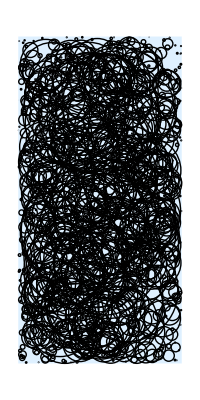

```mathematica
showRandomCircles[a,1.1,2.2]
```

```mathematica
s=uRandomCircles[7,1,3]
```

{{{0.539981,-1.69438},0.116671},{{0.0963987,-1.54301},0.236668},{{0.352946,-1.11543},0.295436},{{0.694789,-0.808602},0.248954},{{-0.140637,2.99194},0.00237205},{{-0.311556,0.786183},0.220186},{{0.691984,-0.708746},0.294747}}

10

8

6

4

-2

0

4

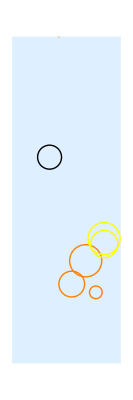

```mathematica
uColorOverlappingCircles[s,1,3]
```

```mathematica
uColorOverlappingCircles[c,1,3]
```

$Aborted

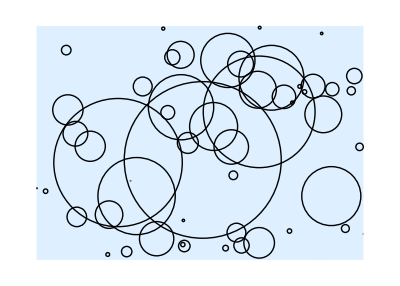

```mathematica
showRandomCircles[c,6,4.3]
```

### Part (iii)

```mathematica
uRemoveCircles[circlelist_,pt_]:=
	Module[{clist = circlelist , x= pt[[1]],y=pt[[2]],i=1,finallist={}},
			While[i≤ Length[circlelist],				
					If[ 
		                                     (circlelist[[i,1,1]] +circlelist[[i,2]] >x>
                                                       circlelist[[i,1,1]] -circlelist[[i,2]])  ||  (circlelist[[i,1,1]] +circlelist[[i,2]] <x<
                                                       circlelist[[i,1,1]] -circlelist[[i,2]])  ||
					(circlelist[[i,1,2]] +circlelist[[i,2]] >y>
                                                       circlelist[[i,1,2]] -circlelist[[i,2]])||(circlelist[[i,1,2]] +circlelist[[i,2]] <y<
                                                       circlelist[[i,1,2]] -circlelist[[i,2]]),,
			                           AppendTo[finallist,circlelist[[i]]  ]
];
Print[circlelist[[i,1,1]] -circlelist[[i,2]] ]
Print[circlelist[[i,1,1]] +circlelist[[i,2]] ]
i++;
];
Return[finallist]
]
```

#### Test Cases for (iii)

### Part (iv)

```mathematica
uColorOverlappingCircles[circlelist_,xbound_, ybound_]:=
Module[{list = circlelist,x = xbound,glist ={},
	y = ybound,i=1,colorList={Black,Blue,Red,Green,Yellow,Purple,Orange},color={},temp,color2},
		AppendTo[glist,{
				Graphics[
					{LightBlue,Rectangle[{-x,-y},{x,y}]}
					]
					}
		];
		While[i≤ Length[list],
temp=intersections[i,circlelist];
AppendTo[color,temp];
Print[temp];
If[temp ≥ 5,color2=Orange,color2=colorList[[temp+1]]];
			AppendTo[glist,
			{
			Graphics[
		{color2, Circle[circlelist[[i,1]],circlelist[[i,2]]]}
				]
			}
				]		
			i++;
			];
Show[{glist}]
]
```

```mathematica
check[circlelist_,i_]:=Module[{count=0,j},
If[EuclideanDistance[circlelist[[i,1]],circlelist[[j,1]]]≤ circlelist[[i,2]]+circlelist[[i,2]],count++];
E
]
```

#### Test Cases for (iv)

```mathematica
intersections[27,b]
```

2

## Problem 3.

(i) Write function uRegPoly[length,n] which has two positive parameters; n is an integer. The function returns the display of  a regular n-sided polygon with sidelength length and the origin as the center. Note that length is not the distance from the center of the polygon to the boundary. It is the length of each of the sides. 

(ii) Create function uRegPyram[length,n,height] which has three positive parameters; n is an integer. The function returns the display of a regular n-sided pyramid of height height  with the base being a regular n-sided polygon with sidelength length and the origin as the center.

(iii) Create function uTwoRegPyram[length,n,height] which has three positive parameters; n is an integer. The function returns the display of two regular n-sided pyramids as in part (ii) that are glued together along their bases, so one of the pyramids is upside down.

### Part (i)

```mathematica
uRegPoly[length_,n_]:=
Graphics[ (*Graphics to display the object*)
Polygon[(*Polygon takes the list we create with "Table"*)
Table[{√(length^2/(2-Cos[π-(π(n-2))/n]))*Cos[(2π k)/n],√(length^2/(2-Cos[π-(π(n-2))/n]))*Sin[(2π k)/n]},(*Creates the points by vectors. The length from the center to the point on the corner is the same as the length of the side because the shapes can be made with equilateral triangles.*)
{k,0,n-1}]
],PlotRange->{-10,10}(*Allows us to see the shape change size*)
]
```

#### Test Cases for (i)

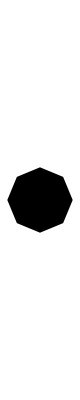

```mathematica
uRegPoly[4,8]
```

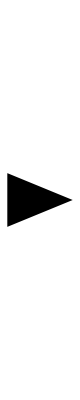

```mathematica
uRegPoly[3,3]
```

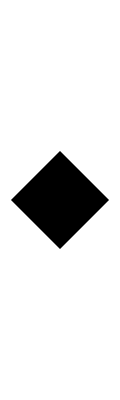

```mathematica
uRegPoly[3,4]
```

### Part (ii)

```mathematica
uRegPyram[length_,n_,height_]:=Module[{a=Table[{√(length^2/(2-Cos[π-(π(n-2))/n]))*Cos[(2π k)/n],√(length^2/(2-Cos[π-(π(n-2))/n]))*Sin[(2π k)/n],0},{k,0,n-1}]},
(*Creates the points by vectors. The length from the center to the point on the corner is the same as the length of the side because the shapes can be made with equilateral triangles.*)
Show[
Graphics3D[
Polygon[
Tuples[(*Arranges the list in all orders to connect every point to another*)
AppendTo[a,{0,0,height}],3](*Adds the point for height*)
]
],Boxed-> False
]
]
```

#### Test Cases for (ii)

```mathematica
uRegPyram[1.5,4,1.5]
```

-Graphics3D-

```mathematica
uRegPyram[2.4,21,4.5]
```

-Graphics3D-

```mathematica
uRegPyram[5.6,6,34]
```

-Graphics3D-

### Part (iii)

```mathematica
uTwoRegPyram[length_,n_,height_]:=Module[{a=Table[{√(length^2/(2-Cos[π-(π(n-2))/n]))*Cos[(2π k)/n],√(length^2/(2-Cos[π-(π(n-2))/n]))*Sin[(2π k)/n],0},{k,0,n-1}],
(*Creates the points by vectors. The length from the center to the point on the corner is the same as the length of the side because the shapes can be made with equilateral triangles.*)
b},
b=AppendTo[a,{0,0,height}];(*Adds the point for height of the top pyramid*)
Show[
Graphics3D[
Polygon[
Tuples[(*Arranges the list in all orders to connect every point to another*)
AppendTo[b,{0,0,-1*height}],3](*Adds the point for the height of the bottom pyramid*)
]
],Boxed-> False
]
]
```

#### Test Cases for (iii)

```mathematica
uTwoRegPyram[25,30,20]
```

-Graphics3D-

```mathematica
uTwoRegPyram[79,4,10]
```

-Graphics3D-

```mathematica
uTwoRegPyram[20,5,15]
```

-Graphics3D-